# Physics 144: Introduction to Numeric Differential Equations in Mathematica (2021) - Version 3

## Background

Differential equations are used extensively in all fields of science and engineering. In physics we often encounter differential equations as the equations of motion of a system. These equations govern the system’s dynamics, i.e. how it evolves in time. These equations of motion can be derived in a variety of ways, the most familiar approach being via Newton’s laws. As an example, let us consider the well-known simple harmonic oscillator, which is just a mass connected to a spring.

-Graphics-

When the mass is at position x(t), the spring force acting on it is F(x(t))=-k x(t), where k is the spring constant. By Newton's second law the mass's acceleration a(t) satisfies

m a(t)=-k x(t).

Since a(t)=x''(t) we can also write this as

m x''(t)=-k x(t).

This is the mass's equation of motion. It is also a differential equation for the function x(t), since it contains both x(t) and the second order time derivative of x(t). In order to predict how the mass will move we need both the equation of motion (which only tells us how things change), and also the initial conditions (which only tell us how things looked initially). Here the initial conditions take the form of the mass's initial position x(0) and initial velocity x'(0) at time t=0. The combination of the differential equation and the initial conditions define what is known as an initial value problem. Remember that the solution of this problem is the function x(t) which satisfies both the equation of motion as well as the initial conditions. In some cases these problems can be solved by hand, but for many important examples this is simply impossible. Luckily, there are numeric methods available for solving these types of problems on a computer. Of course, this does not produce an analytic expression for x(t), but does allow us to calculate the numeric value of x(t) for a given value of t.

```mathematica
Clear[Derivative]; ClearAll["Global`*"]; (*Run if you want to clear all definitions.*)
```

## 1D Example - NDSolve

In Mathematica we can use NDSolve to solve differential equations numerically. This function is very easy to use, but the differential equation and initial conditions must be written in a very specific form. Let us consider the harmonic oscillator with k=2, m=3 and initial conditions x(0)=-3 and x'(0)=5. To solve this initial value problem we use NDSolve as follows:

```mathematica
(*Clear the names of the functions in the differential equation and the independent variable.*)
Clear[Derivative]; ClearAll[x,t,m,k];
(*Set the mass and spring constant.*)
m=3;
k=2;
(*Solve the EOM with the desired initial conditions. Note the double == equal signs!*)
solution=NDSolve[{m x''[t]==-k x[t],x[0]==-3,x'[0]==-5},x,{t,0,40}]; 
 (*Assign the solution to the function x.*)
x=x/.solution[[1]];
```

Pay close attention to the notation used in NDSolve. The first argument is a list containing the differential equation and the initial conditions. NOTE THE DOUBLE == EQUAL SIGNS. The second argument is the name of the function to be solved for. The third argument is the name and range of the independent variable, which is t in this case. NDSolve only finds the values of x(t) between t=0 and t=40. We can now use the function x(t) in the usual way:

```mathematica
(*Where is the mass at t=1.3?*)
x[1.3]
```

-6.80922

```mathematica
(*If we ask for x at t=41 it complains. We only solved the equation up to t=40.*)
x[41]
```

InterpolatingFunction::dmval: Input value {41} lies outside the range of data in the interpolating function. Extrapolation will be used.

-3.99827

```mathematica
(*Are the initial conditions satisfied?*)
x[0] (*Should be -3.*)
x'[0] (*Should be -5.*)
```

-3.

-5.

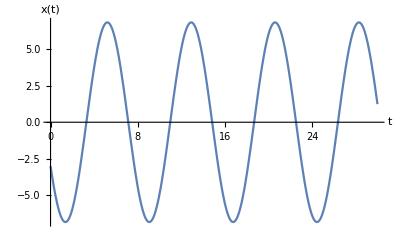

```mathematica
(*Make a plot of x(t) vs t. We see the expected periodic oscillations.*)
Plot[x[t],{t,0,30},AxesLabel->{"t","x(t)"},LabelStyle->{12,Black}]
```

```mathematica
Clear[Derivative]; ClearAll["Global`*"]; (*Run if you want to clear all definitions.*)
```

## 2D Example - NDSolve

Consider a particle moving in two dimensions while experiencing the position-dependent force

F⃗(x(t),y(t))=F_x(x(t),y(t))î+F_y(x(t),y(t))ĵ.

Newton's second law is now a vector equation, which we can split into two scalar equations for the two directions. This produces the set of differential equations

m x''(t)=F_x(x(t),y(t))   and   m y''(t)=F_y(x(t),y(t)).

This is already a much more difficult problem than the 1D case, since now we must solve both differential equations simultaneously. We cannot consider only one direction at a time, since the acceleration in the x direction depends on the particle’s y coordinate, and vice-versa. Luckily, Mathematica has no problem with this. Below we solve this problem for a particular choice of the force and initial conditions. We take m=3.

### Note: If you want to use the code below, copy the entire cell, including the ClearAll and Clear at the top. The code lazily reuses the same variable names for different purposes, and without the ClearAll and Clear this will cause problems.

```mathematica
(*Clear the definitions of the functions in the differential equation and the independent variable.*)
ClearAll[Fx,Fy,x,y,m,t];Clear[Derivative];
(*Set the mass.*)
m=3;
(*Define the two component of the force as functions of position.*)
Fx[x_,y_]=-2 x Sqrt[(x^2+y^2)];
Fy[x_,y_]=-2 y Sqrt[(x^2+y^2)];
(*Solve the EOM with the desired initial conditions. Note the double == equal signs!*)
solution=NDSolve[{m x''[t]==Fx[x[t],y[t]],m y''[t]==Fy[x[t],y[t]],x[0]==0,y[0]==5,x'[0]==5,y'[0]==9},{x,y},{t,0,40}];
 (*Assign the solutions to the functions x and y.*)
{x,y}={x,y}/.solution[[1]];
```

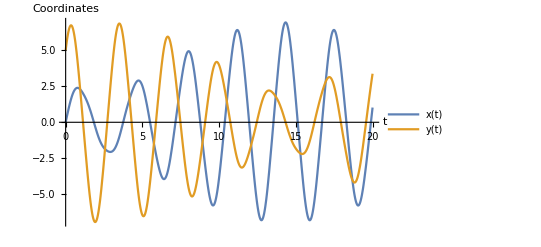

```mathematica
(*Make a plot of x(t) and y(t) vs t.*)
Plot[{x[t],y[t]},{t,0,20},AxesLabel->{"t","Coordinates"},LabelStyle->{12,Black},PlotLegends->"Expressions"]
```

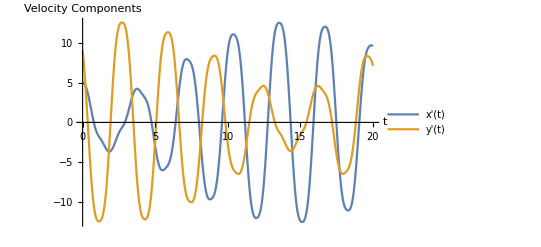

```mathematica
(*Make a plot of the x and y components of the velocity vs t.*)
Plot[{x'[t],y'[t]},{t,0,20},AxesLabel->{"t","Velocity Components"},LabelStyle->{12,Black},PlotLegends->"Expressions"]
```

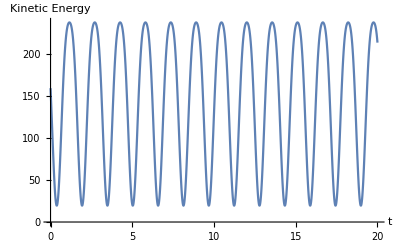

```mathematica
(*Define the particle's kinetic energy as a function of time and plot it.*)
KE[t_]=(m/2)(x'[t]^2+y'[t]^2);
Plot[KE[t],{t,0,20},AxesLabel->{"t","Kinetic Energy"},LabelStyle->{12,Black}]
```

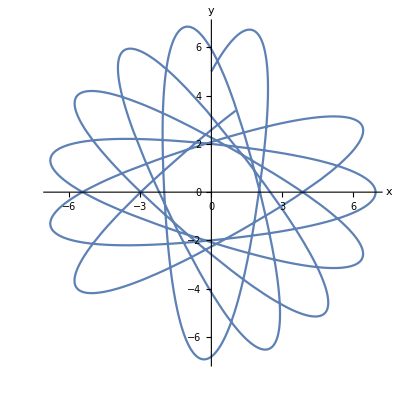

```mathematica
(*Plot the particle's trajectory in the x-y plane.*)
plot1=ParametricPlot[{x[t],y[t]},{t,0,20},AxesLabel->{"x","y"},LabelStyle->{12,Black},PlotRange->All]
```

```mathematica
(*Animate the particle's trajectory in the x-y plane. First plot the trajectory and then combine with animation. Some trickery with With[] is needed to ensure that the animation does not break when we reassign x and y.*)
pathplot=ParametricPlot[{x[t],y[t]},{t,0,15}];
With[{pathplot=pathplot,x=x,y=y},Animate[Show[pathplot,ListPlot[{{x[t],y[t]}},PlotMarkers->{Automatic,20}],AxesLabel->{"x","y"},LabelStyle->{12,Black},PlotRange->All,AspectRatio->Automatic],{t,0,15},AnimationRepetitions->3,AnimationRunning->False]]
```